```mathematica
f[z_]:=z/(1-z)^2
```

```mathematica
lis = List[];
For[i=0,i<100000,i++,zz = RandomComplex[{-1-I,1+I}];If[Abs[zz]<1, lis=Append[lis, f[zz]]]]
```

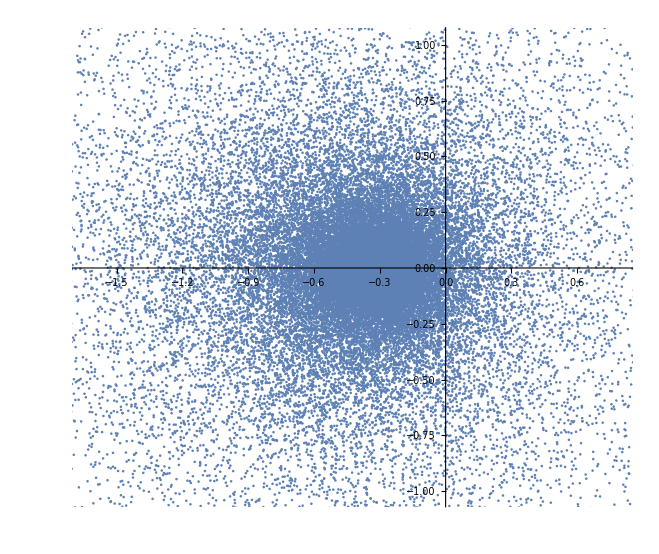

```mathematica
ComplexListPlot[lis]
```

```mathematica
f2[z_]:=z/(1-z)
```

```mathematica
lis2 = List[];
For[i=0,i<10000,i++,zz =RandomComplex[{-1-I,1+I}];If[Abs[zz]<1, lis2=Append[lis2, f2[zz]]]]
```

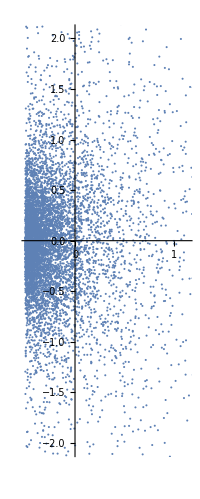

```mathematica
ComplexListPlot[lis2]
```

```mathematica
lis3 = List[];
For[i=0,i<10000,i++,zz = RandomComplex[{-1-I,1+I}];If[Abs[zz]<1, lis3=Append[lis3, zz]]]
```

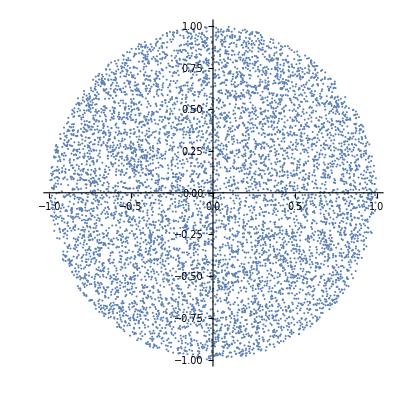

```mathematica
ComplexListPlot[lis3]
```

```mathematica
ComplexListPlot[lis2]
```